```mathematica
Quit[];
```

```mathematica
eq1=f'[r]+(-4 ep+4 f[r]+2 r^2 V[ph[r]]+r^2 f[r] ph'[r]^2)/(4 r);
eq2=1/(2 r f[r])(2 ep ph'[r]+2 f[r] ph'[r]-r^2 V[ph[r]] ph'[r]-2 r V'[ph[r]])+ph''[r];
eq3=h'[r]-(h[r] (4 ep-4 f[r]-2 r^2 V[ph[r]]+r^2 f[r] ph'[r]^2))/(4 r f[r]);
```

```mathematica
if[r_]:=f1 *(r-r0) + f2 *(r-r0)^2 +f3 *(r-r0)^3+f4 *(r-r0)^4+f5 *(r-r0)^5
ih[r_]:=(r-r0) + h2 *(r-r0)^2 +h3 *(r-r0)^3+h4 *(r-r0)^4+h5 *(r-r0)^5
iph[r_]:=ph0 + ph1 *(r-r0) + ph2 *(r-r0)^2 +ph3 *(r-r0)^3+ph4 *(r-r0)^4+ph5 *(r-r0)^5
```

```mathematica
V[x_]:=-g5 x^5 -g7 x^7
ep=1;
```

```mathematica
f1=(2+g5 ph0^5 r0^2+g7 ph0^7 r0^2)/(2 r0);
ph1=-(2 (5 g5 ph0^4 r0+7 g7 ph0^6 r0))/(2+g5 ph0^5 r0^2+g7 ph0^7 r0^2);
f2=-((8+4 g5 ph0^5 r0^2+4 g7 ph0^7 r0^2+75 g5^2 ph0^8 r0^4+210 g5 g7 ph0^10 r0^4+147 g7^2 ph0^12 r0^4)/(8 r0^2+4 g5 ph0^5 r0^4+4 g7 ph0^7 r0^4));ph2=(ph0^7 (5 g5+7 g7 ph0^2) r0^2 (g5^2 ph0^5 (-5+ph0^2) r0^2+g7 ph0^2 (84+2 ph0^2-7 g7 ph0^7 r0^2+g7 ph0^9 r0^2)+2 g5 (20+ph0^2-4 g7 ph0^7 r0^2+g7 ph0^9 r0^2)))/(2+g5 ph0^5 r0^2+g7 ph0^7 r0^2)^3;h2=(-8-4 g7 ph0^7 r0^2+25 g5^2 ph0^8 r0^4+49 g7^2 ph0^12 r0^4+2 g5 ph0^5 r0^2 (-2+35 g7 ph0^5 r0^2))/(2 r0 (2+g5 ph0^5 r0^2+g7 ph0^7 r0^2)^2);
f3=1/(12 r0^3 (2+g5 ph0^5 r0^2+g7 ph0^7 r0^2)^3)(96+160 g7 ph0^7 r0^2+4 g7^2 ph0^12 (-49+24 ph0^2) r0^4+4 g7^3 ph0^17 (10290+49 ph0^2+6 ph0^4) r0^6+g5^4 ph0^16 (3125+75 ph0^2+2 ph0^4) r0^8+g7^4 ph0^24 (13377+147 ph0^2+2 ph0^4) r0^8+4 g5^3 ph0^11 r0^6 (2500+25 ph0^2+6 ph0^4+4750 g7 ph0^7 r0^2+90 g7 ph0^9 r0^2+2 g7 ph0^11 r0^2)+2 g5^2 ph0^8 r0^4 (-50+48 ph0^2+24500 g7 ph0^5 r0^2+190 g7 ph0^7 r0^2+36 g7 ph0^9 r0^2+20825 g7^2 ph0^12 r0^4+321 g7^2 ph0^14 r0^4+6 g7^2 ph0^16 r0^4)+4 g5 ph0^5 r0^2 (40+2 g7 ph0^5 (-35+24 ph0^2) r0^2+g7^2 ph0^10 (19600+119 ph0^2+18 ph0^4) r0^4+2 g7^3 ph0^17 (4900+63 ph0^2+ph0^4) r0^6));ph3=-1/(9 r0 (2+g5 ph0^5 r0^2+g7 ph0^7 r0^2)^5)ph0^4 (5 g5+7 g7 ph0^2) (32+48 g7 ph0^5 (-14+ph0^2) r0^2+12 g7^2 ph0^10 (3136+175 ph0^2+4 ph0^4) r0^4+14 g7^3 ph0^17 (-1722+81 ph0^2+2 ph0^4) r0^6+3 g7^4 ph0^24 (49-14 ph0^2+2 ph0^4) r0^8+g5^4 ph0^16 (125-30 ph0^2+6 ph0^4) r0^8+2 g5^3 ph0^11 r0^6 (-3500+275 ph0^2+14 ph0^4+245 g7 ph0^7 r0^2-54 g7 ph0^9 r0^2+12 g7 ph0^11 r0^2)+2 g5^2 ph0^6 r0^4 (4000+530 ph0^2+24 ph0^4-14270 g7 ph0^7 r0^2+1105 g7 ph0^9 r0^2+42 g7 ph0^11 r0^2+244 g7^2 ph0^14 r0^4-84 g7^2 ph0^16 r0^4+18 g7^2 ph0^18 r0^4)+2 g5 ph0^3 r0^2 (-160+24 ph0^2+18480 g7 ph0^5 r0^2+1508 g7 ph0^7 r0^2+48 g7 ph0^9 r0^2-21504 g7^2 ph0^12 r0^4+1397 g7^2 ph0^14 r0^4+42 g7^2 ph0^16 r0^4+63 g7^3 ph0^19 r0^6-66 g7^3 ph0^21 r0^6+12 g7^3 ph0^23 r0^6));h3=1/(6 r0^2 (2+g5 ph0^5 r0^2+g7 ph0^7 r0^2)^4)(96+160 g7 ph0^7 r0^2+4 g7^2 ph0^12 (-343+24 ph0^2) r0^4+4 g7^3 ph0^17 (-2058-245 ph0^2+6 ph0^4) r0^6+g7^4 ph0^24 (3087-147 ph0^2+2 ph0^4) r0^8+g5^4 ph0^16 (875-75 ph0^2+2 ph0^4) r0^8+4 g5^3 ph0^11 r0^6 (-500-125 ph0^2+6 ph0^4+1150 g7 ph0^7 r0^2-90 g7 ph0^9 r0^2+2 g7 ph0^11 r0^2)+2 g5^2 ph0^8 r0^4 (-350+48 ph0^2-4900 g7 ph0^5 r0^2-950 g7 ph0^7 r0^2+36 g7 ph0^9 r0^2+4655 g7^2 ph0^12 r0^4-321 g7^2 ph0^14 r0^4+6 g7^2 ph0^16 r0^4)+4 g5 ph0^5 r0^2 (40+2 g7 ph0^5 (-245+24 ph0^2) r0^2+g7^2 ph0^10 (-3920-595 ph0^2+18 ph0^4) r0^4+2 g7^3 ph0^17 (1078-63 ph0^2+ph0^4) r0^6));
f4=-((4608+12288 g7 ph0^7 r0^2+4480 g7^2 ph0^12 (7+3 ph0^2) r0^4+384 g7^3 ph0^17 (-1715+147 ph0^2+20 ph0^4) r0^6+12 g7^4 ph0^22 (3361400+27097 ph0^2+3626 ph0^4+200 ph0^6) r0^8+8 g7^5 ph0^29 (2319366+69972 ph0^2+2107 ph0^4+48 ph0^6) r0^10+3 g7^6 ph0^36 (789929+38759 ph0^2+882 ph0^4+8 ph0^6) r0^12+g5^6 ph0^24 (191875+28125 ph0^2+1350 ph0^4+24 ph0^6) r0^12+2 g5^5 ph0^19 r0^10 (890000+70000 ph0^2+4300 ph0^4+192 ph0^6+1086375 g7 ph0^7 r0^2+111375 g7 ph0^9 r0^2+4590 g7 ph0^11 r0^2+72 g7 ph0^13 r0^2)+g5^4 ph0^14 r0^8 (4480000+87500 ph0^2+22200 ph0^4+2400 ph0^6+16226000 g7 ph0^7 r0^2+948000 g7 ph0^9 r0^2+49880 g7 ph0^11 r0^2+1920 g7 ph0^13 r0^2+8978725 g7^2 ph0^14 r0^4+721275 g7^2 ph0^16 r0^4+25866 g7^2 ph0^18 r0^4+360 g7^2 ph0^20 r0^4)+4 g5^3 ph0^11 r0^6 (-40000+7200 ph0^2+1920 ph0^4+8134000 g7 ph0^5 r0^2+119500 g7 ph0^7 r0^2+26640 g7 ph0^9 r0^2+2400 g7 ph0^11 r0^2+13592600 g7^2 ph0^12 r0^4+633200 g7^2 ph0^14 r0^4+28724 g7^2 ph0^16 r0^4+960 g7^2 ph0^18 r0^4+4562145 g7^3 ph0^19 r0^6+306225 g7^3 ph0^21 r0^6+9666 g7^3 ph0^23 r0^6+120 g7^3 ph0^25 r0^6)+g5^2 ph0^8 r0^4 (16000+13440 ph0^2-784000 g7 ph0^5 r0^2+109440 g7 ph0^7 r0^2+23040 g7 ph0^9 r0^2+85338400 g7^2 ph0^10 r0^4+989800 g7^2 ph0^12 r0^4+190032 g7^2 ph0^14 r0^4+14400 g7^2 ph0^16 r0^4+85832320 g7^3 ph0^17 r0^6+3339840 g7^3 ph0^19 r0^6+131408 g7^3 ph0^21 r0^6+3840 g7^3 ph0^23 r0^6+19672765 g7^4 ph0^24 r0^8+1152627 g7^4 ph0^26 r0^8+32346 g7^4 ph0^28 r0^8+360 g7^4 ph0^30 r0^8)+2 g5 ph0^5 r0^2 (6144+4480 g7 ph0^5 (5+3 ph0^2) r0^2+64 g7^2 ph0^10 (-9800+1071 ph0^2+180 ph0^4) r0^4+8 g7^3 ph0^15 (6050520+57575 ph0^2+9324 ph0^4+600 ph0^6) r0^6+4 g7^4 ph0^22 (8067360+271852 ph0^2+9331 ph0^4+240 ph0^6) r0^8+3 g7^5 ph0^29 (1798349+95109 ph0^2+2394 ph0^4+24 ph0^6) r0^10))/(144 r0^4 (2+g5 ph0^5 r0^2+g7 ph0^7 r0^2)^5));ph4=1/(36 r0^2 (2+g5 ph0^5 r0^2+g7 ph0^7 r0^2)^7)ph0^4 (5 g5+7 g7 ph0^2) (384+1344 g7 ph0^5 (4+ph0^2) r0^2+64 g7^2 ph0^10 (-3969-154 ph0^2+27 ph0^4) r0^4+24 g7^3 ph0^15 (333396+45080 ph0^2+287 ph0^4+50 ph0^6) r0^6+12 g7^4 ph0^22 (-1093484+21903 ph0^2+1379 ph0^4+44 ph0^6) r0^8+2 g7^5 ph0^29 (1026942-85701 ph0^2+2387 ph0^4+72 ph0^6) r0^10+3 g7^6 ph0^36 (4459-98 ph0^2-35 ph0^4+6 ph0^6) r0^12+g5^6 ph0^24 (1375+150 ph0^2-75 ph0^4+18 ph0^6) r0^12+2 g5^5 ph0^19 r0^10 (188500-25325 ph0^2+1165 ph0^4+72 ph0^6+4650 g7 ph0^7 r0^2+390 g7 ph0^9 r0^2-210 g7 ph0^11 r0^2+54 g7 ph0^13 r0^2)+g5^4 ph0^14 r0^8 (-1696000+44500 ph0^2+8300 ph0^4+528 ph0^6+2377300 g7 ph0^7 r0^2-305850 g7 ph0^9 r0^2+13958 g7 ph0^11 r0^2+720 g7 ph0^13 r0^2+28235 g7^2 ph0^14 r0^4+534 g7^2 ph0^16 r0^4-1035 g7^2 ph0^18 r0^4+270 g7^2 ph0^20 r0^4)+4 g5^3 ph0^9 r0^6 (184000+66400 ph0^2+870 ph0^4+300 ph0^6-2725600 g7 ph0^7 r0^2+88520 g7 ph0^9 r0^2+10110 g7 ph0^11 r0^2+528 g7 ph0^13 r0^2+1537090 g7^2 ph0^14 r0^4-191027 g7^2 ph0^16 r0^4+8167 g7^2 ph0^18 r0^4+360 g7^2 ph0^20 r0^4+14852 g7^3 ph0^21 r0^6-588 g7^3 ph0^23 r0^6-360 g7^3 ph0^25 r0^6+90 g7^3 ph0^27 r0^6)+g5^2 ph0^6 r0^4 (-54400-5120 ph0^2+1728 ph0^4+5510400 g7 ph0^5 r0^2+1288480 g7 ph0^7 r0^2+13368 g7 ph0^9 r0^2+3600 g7 ph0^11 r0^2-26892880 g7^2 ph0^12 r0^4+856856 g7^2 ph0^14 r0^4+72528 g7^2 ph0^16 r0^4+3168 g7^2 ph0^18 r0^4+8356208 g7^3 ph0^19 r0^6-983228 g7^3 ph0^21 r0^6+37556 g7^3 ph0^23 r0^6+1440 g7^3 ph0^25 r0^6+86933 g7^4 ph0^26 r0^8-4230 g7^4 ph0^28 r0^8-1185 g7^4 ph0^30 r0^8+270 g7^4 ph0^32 r0^8)+2 g5 ph0^3 r0^2 (1280+672 ph0^2-124320 g7 ph0^5 r0^2-6976 g7 ph0^7 r0^2+1728 g7 ph0^9 r0^2+5985840 g7^2 ph0^10 r0^4+1026704 g7^2 ph0^12 r0^4+8388 g7^2 ph0^14 r0^4+1800 g7^2 ph0^16 r0^4-15149232 g7^3 ph0^17 r0^6+407456 g7^3 ph0^19 r0^6+28468 g7^3 ph0^21 r0^6+1056 g7^3 ph0^23 r0^6+3094056 g7^4 ph0^24 r0^8-322861 g7^4 ph0^26 r0^8+10645 g7^4 ph0^28 r0^8+360 g7^4 ph0^30 r0^8+32046 g7^5 ph0^31 r0^10-1134 g7^5 ph0^33 r0^10-270 g7^5 ph0^35 r0^10+54 g7^5 ph0^37 r0^10));h4=-1/(72 r0^3 (2+g5 ph0^5 r0^2+g7 ph0^7 r0^2)^6)(4608+12288 g7 ph0^7 r0^2+896 g7^2 ph0^12 (-56+15 ph0^2) r0^4+192 g7^3 ph0^17 (-4802-539 ph0^2+40 ph0^4) r0^6-12 g7^4 ph0^22 (480200+31899 ph0^2+6174 ph0^4-200 ph0^6) r0^8+8 g7^5 ph0^29 (792330+20580 ph0^2-2695 ph0^4+48 ph0^6) r0^10+3 g7^6 ph0^36 (-228095+20923 ph0^2-686 ph0^4+8 ph0^6) r0^12+g5^6 ph0^24 (-113125+17625 ph0^2-1050 ph0^4+24 ph0^6) r0^12+2 g5^5 ph0^19 r0^10 (430000+26000 ph0^2-5500 ph0^4+192 ph0^6-431625 g7 ph0^7 r0^2+64275 g7 ph0^9 r0^2-3570 g7 ph0^11 r0^2+72 g7 ph0^13 r0^2)+g5^4 ph0^14 r0^8 (-640000-78500 ph0^2-37800 ph0^4+2400 ph0^6+6262000 g7 ph0^7 r0^2+304800 g7 ph0^9 r0^2-63800 g7 ph0^11 r0^2+1920 g7 ph0^13 r0^2-2788675 g7^2 ph0^14 r0^4+393855 g7^2 ph0^16 r0^4-20118 g7^2 ph0^18 r0^4+360 g7^2 ph0^20 r0^4)+4 g5^3 ph0^11 r0^6 (-56000-13200 ph0^2+1920 ph0^4-1162000 g7 ph0^5 r0^2-132100 g7 ph0^7 r0^2-45360 g7 ph0^9 r0^2+2400 g7 ph0^11 r0^2+4610200 g7^2 ph0^12 r0^4+184720 g7^2 ph0^14 r0^4-36740 g7^2 ph0^16 r0^4+960 g7^2 ph0^18 r0^4-1227135 g7^3 ph0^19 r0^6+162093 g7^3 ph0^21 r0^6-7518 g7^3 ph0^23 r0^6+120 g7^3 ph0^25 r0^6)+g5^2 ph0^8 r0^4 (-25600+13440 ph0^2-1097600 g7 ph0^5 r0^2-200640 g7 ph0^7 r0^2+23040 g7 ph0^9 r0^2-12191200 g7^2 ph0^10 r0^4-1213240 g7^2 ph0^12 r0^4-323568 g7^2 ph0^14 r0^4+14400 g7^2 ph0^16 r0^4+27487040 g7^3 ph0^17 r0^6+931392 g7^3 ph0^19 r0^6-168080 g7^3 ph0^21 r0^6+3840 g7^3 ph0^23 r0^6-4997755 g7^4 ph0^24 r0^8+604023 g7^4 ph0^26 r0^8-25158 g7^4 ph0^28 r0^8+360 g7^4 ph0^30 r0^8)+2 g5 ph0^5 r0^2 (6144+4480 g7 ph0^5 (-8+3 ph0^2) r0^2+32 g7^2 ph0^10 (-27440-3927 ph0^2+360 ph0^4) r0^4+8 g7^3 ph0^15 (-864360-71981 ph0^2-15876 ph0^4+600 ph0^6) r0^6+4 g7^4 ph0^22 (2593080+76244 ph0^2-11935 ph0^4+240 ph0^6) r0^8+3 g7^5 ph0^29 (-468195+50225 ph0^2-1862 ph0^4+24 ph0^6) r0^10));
f5=(30720+112640 g7 ph0^7 r0^2+8960 g7^2 ph0^12 (21+20 ph0^2) r0^4+8064 g7^3 ph0^17 (588+77 ph0^2+20 ph0^4) r0^6+112 g7^4 ph0^22 (-1317120+60319 ph0^2+7350 ph0^4+800 ph0^6) r0^8+1568 g7^5 ph0^27 (3278394+57918 ph0^2+4424 ph0^4+369 ph0^6+20 ph0^8) r0^10+112 g7^6 ph0^34 (18929484+1463238 ph0^2+45913 ph0^4+2079 ph0^6+60 ph0^8) r0^12+8 g7^7 ph0^41 (42504903+6281016 ph0^2+229467 ph0^4+6468 ph0^6+100 ph0^8) r0^14+5 g5^8 ph0^32 (-30625+86000 ph0^2+10975 ph0^4+510 ph0^6+8 ph0^8) r0^16+g7^8 ph0^48 (23143239+4725168 ph0^2+225351 ph0^4+4998 ph0^6+40 ph0^8) r0^16+20 g5^7 ph0^27 r0^14 (102500+263500 ph0^2+22600 ph0^4+1320 ph0^6+40 ph0^8+339125 g7 ph0^7 r0^2+268300 g7 ph0^9 r0^2+27135 g7 ph0^11 r0^2+1122 g7 ph0^13 r0^2+16 g7 ph0^15 r0^2)+8 g5^6 ph0^22 r0^12 (7700000+2412500 ph0^2+158000 ph0^4+14850 ph0^6+840 ph0^8+15080625 g7 ph0^7 r0^2+6969250 g7 ph0^9 r0^2+499475 g7 ph0^11 r0^2+25740 g7 ph0^13 r0^2+700 g7 ph0^15 r0^2+8362375 g7^2 ph0^14 r0^4+3425050 g7^2 ph0^16 r0^4+289915 g7^2 ph0^18 r0^4+10761 g7^2 ph0^20 r0^4+140 g7^2 ph0^22 r0^4)+4 g5^5 ph0^17 r0^10 (63600000+3180000 ph0^2+419000 ph0^4+73800 ph0^6+7840 ph0^8+235610000 g7 ph0^7 r0^2+43215000 g7 ph0^9 r0^2+2479900 g7 ph0^11 r0^2+201960 g7 ph0^13 r0^2+10080 g7 ph0^15 r0^2+218118500 g7^2 ph0^14 r0^4+60641400 g7^2 ph0^16 r0^4+3736420 g7^2 ph0^18 r0^4+171336 g7^2 ph0^20 r0^4+4200 g7^2 ph0^22 r0^4+63603325 g7^3 ph0^21 r0^6+19084880 g7^3 ph0^23 r0^6+1400507 g7^3 ph0^25 r0^6+47022 g7^3 ph0^27 r0^6+560 g7^3 ph0^29 r0^6)+2 g5^4 ph0^14 r0^8 (-8240000+805000 ph0^2+210000 ph0^4+44800 ph0^6+1253280000 g7 ph0^5 r0^2+45552000 g7 ph0^7 r0^2+5803200 g7 ph0^9 r0^2+856080 g7 ph0^11 r0^2+78400 g7 ph0^13 r0^2+2375604000 g7^2 ph0^12 r0^4+315874000 g7^2 ph0^14 r0^4+15967480 g7^2 ph0^16 r0^4+1138104 g7^2 ph0^18 r0^4+50400 g7^2 ph0^20 r0^4+1350682900 g7^3 ph0^19 r0^6+283948240 g7^3 ph0^21 r0^6+15349076 g7^3 ph0^23 r0^6+630960 g7^3 ph0^25 r0^6+14000 g7^3 ph0^27 r0^6+256696195 g7^4 ph0^26 r0^8+64186240 g7^4 ph0^28 r0^8+4186819 g7^4 ph0^30 r0^8+128010 g7^4 ph0^32 r0^8+1400 g7^4 ph0^34 r0^8)+4 g5^3 ph0^11 r0^6 (288000+79200 ph0^2+40320 ph0^4-29764000 g7 ph0^5 r0^2+2410000 g7 ph0^7 r0^2+504000 g7 ph0^9 r0^2+89600 g7 ph0^11 r0^2+2348178000 g7^2 ph0^10 r0^4+66144400 g7^2 ph0^12 r0^4+7854960 g7^2 ph0^14 r0^4+985968 g7^2 ph0^16 r0^4+78400 g7^2 ph0^18 r0^4+2836198400 g7^3 ph0^17 r0^6+302456000 g7^3 ph0^19 r0^6+13515976 g7^3 ph0^21 r0^6+850608 g7^3 ph0^23 r0^6+33600 g7^3 ph0^25 r0^6+1099939260 g7^4 ph0^24 r0^8+194294940 g7^4 ph0^26 r0^8+9358528 g7^4 ph0^28 r0^8+347160 g7^4 ph0^30 r0^8+7000 g7^4 ph0^32 r0^8+150123211 g7^5 ph0^31 r0^10+33587372 g7^5 ph0^33 r0^10+1984793 g7^5 ph0^35 r0^10+55590 g7^5 ph0^37 r0^10+560 g7^5 ph0^39 r0^10)+8 g5^2 ph0^8 r0^4 (12000+22400 ph0^2+705600 g7 ph0^5 r0^2+150480 g7 ph0^7 r0^2+60480 g7 ph0^9 r0^2-38964800 g7^2 ph0^10 r0^4+2621500 g7^2 ph0^12 r0^4+449400 g7^2 ph0^14 r0^4+67200 g7^2 ph0^16 r0^4+2122003800 g7^3 ph0^15 r0^6+48884360 g7^3 ph0^17 r0^6+5208112 g7^3 ph0^19 r0^6+563832 g7^3 ph0^21 r0^6+39200 g7^3 ph0^23 r0^6+1758876560 g7^4 ph0^22 r0^8+160379940 g7^4 ph0^24 r0^8+6352948 g7^4 ph0^26 r0^8+355806 g7^4 ph0^28 r0^8+12600 g7^4 ph0^30 r0^8+491732003 g7^5 ph0^29 r0^10+78005746 g7^5 ph0^31 r0^10+3390653 g7^5 ph0^33 r0^10+114180 g7^5 ph0^35 r0^10+2100 g7^5 ph0^37 r0^10+51102884 g7^6 ph0^36 r0^12+10731098 g7^6 ph0^38 r0^12+583296 g7^6 ph0^40 r0^12+15045 g7^6 ph0^42 r0^12+140 g7^6 ph0^44 r0^12)+4 g5 ph0^5 r0^2 (28160+22400 g7 ph0^5 (3+4 ph0^2) r0^2+2016 g7^2 ph0^10 (1120+187 ph0^2+60 ph0^4) r0^4+560 g7^3 ph0^15 (-157878+8799 ph0^2+1260 ph0^4+160 ph0^6) r0^6+56 g7^4 ph0^20 (66648330+1316630 ph0^2+121037 ph0^4+11439 ph0^6+700 ph0^8) r0^8+28 g7^5 ph0^27 (77911764+6386758 ph0^2+224833 ph0^4+11286 ph0^6+360 ph0^8) r0^10+28 g7^6 ph0^34 (16259229+2436868 ph0^2+96635 ph0^4+2970 ph0^6+50 ph0^8) r0^12+g7^7 ph0^41 (37606863+7680456 ph0^2+388913 ph0^4+9282 ph0^6+80 ph0^8) r0^14))/(240 r0^5 (2+g5 ph0^5 r0^2+g7 ph0^7 r0^2)^7);ph5=-1/(900 r0^3 (2+g5 ph0^5 r0^2+g7 ph0^7 r0^2)^9)ph0^4 (5 g5+7 g7 ph0^2) (30720+5120 g7 ph0^5 (63+26 ph0^2) r0^2+512 g7^2 ph0^10 (17346+3563 ph0^2+510 ph0^4) r0^4+128 g7^3 ph0^15 (-3827880-525672 ph0^2+9107 ph0^4+2250 ph0^6) r0^6+16 g7^4 ph0^20 (689067792+190068648 ph0^2+2688777 ph0^4+22498 ph0^6+12160 ph0^8) r0^8+8 g7^5 ph0^27 (-4213927872-82136838 ph0^2+9804753 ph0^4+94402 ph0^6+10560 ph0^8) r0^10+4 g7^6 ph0^34 (3765325032-239075802 ph0^2+2418297 ph0^4+137858 ph0^6+6000 ph0^8) r0^12+2 g7^7 ph0^41 (-418739202+49199577 ph0^2-2476509 ph0^4+53746 ph0^6+2120 ph0^8) r0^14+5 g5^8 ph0^32 (-223625+29275 ph0^2-590 ph0^4-252 ph0^6+72 ph0^8) r0^16+3 g7^8 ph0^48 (-2499441+252791 ph0^2-6762 ph0^4-588 ph0^6+120 ph0^8) r0^16+2 g5^7 ph0^27 r0^14 (-50222500+9175375 ph0^2-736225 ph0^4+26050 ph0^6+2120 ph0^8-4817375 g7 ph0^7 r0^2+616025 g7 ph0^9 r0^2-13680 g7 ph0^11 r0^2-4788 g7 ph0^13 r0^2+1440 g7 ph0^15 r0^2)+2 g5^6 ph0^22 r0^12 (598020000-62537000 ph0^2+794650 ph0^4+135940 ph0^6+12000 ph0^8-430460250 g7 ph0^7 r0^2+76014775 g7 ph0^9 r0^2-5912555 g7 ph0^11 r0^2+208950 g7 ph0^13 r0^2+14840 g7 ph0^15 r0^2-18189975 g7^2 ph0^14 r0^4+2301975 g7^2 ph0^16 r0^4-66528 g7^2 ph0^18 r0^4-16380 g7^2 ph0^20 r0^4+5040 g7^2 ph0^22 r0^4)+2 g5^5 ph0^17 r0^10 (-960640000-68326000 ph0^2+9687700 ph0^4+180520 ph0^6+42240 ph0^8+5111418000 g7 ph0^7 r0^2-523548300 g7 ph0^9 r0^2+8054020 g7 ph0^11 r0^2+944264 g7 ph0^13 r0^2+72000 g7 ph0^15 r0^2-1601950800 g7^2 ph0^14 r0^4+272996875 g7^2 ph0^16 r0^4-20679813 g7^2 ph0^18 r0^4+707746 g7^2 ph0^20 r0^4+44520 g7^2 ph0^22 r0^4-39383615 g7^3 ph0^21 r0^6+5188545 g7^3 ph0^23 r0^6-193000 g7^3 ph0^25 r0^6-33012 g7^3 ph0^27 r0^6+10080 g7^3 ph0^29 r0^6)+2 g5^4 ph0^12 r0^8 (215680000+174272000 ph0^2+6010600 ph0^4+65360 ph0^6+97280 ph0^8-8602336000 g7 ph0^7 r0^2-391537400 g7 ph0^9 r0^2+66127860 g7 ph0^11 r0^2+1097992 g7 ph0^13 r0^2+211200 g7 ph0^15 r0^2+18524799600 g7^2 ph0^14 r0^4-1836755700 g7^2 ph0^16 r0^4+29512382 g7^2 ph0^18 r0^4+2693372 g7^2 ph0^20 r0^4+180000 g7^2 ph0^22 r0^4-3364813870 g7^3 ph0^21 r0^6+555213115 g7^3 ph0^23 r0^6-40763847 g7^3 ph0^25 r0^6+1316230 g7^3 ph0^27 r0^6+74200 g7^3 ph0^29 r0^6-54908264 g7^4 ph0^28 r0^8+7975994 g7^4 ph0^30 r0^8-338838 g7^4 ph0^32 r0^8-42840 g7^4 ph0^34 r0^8+12600 g7^4 ph0^36 r0^8)+2 g5^3 ph0^9 r0^6 (-22912000-8166400 ph0^2+259520 ph0^4+144000 ph0^6+2295552000 g7 ph0^5 r0^2+1234620800 g7 ph0^7 r0^2+31844480 g7 ph0^9 r0^2+424896 g7 ph0^11 r0^2+389120 g7 ph0^13 r0^2-30500971200 g7^2 ph0^12 r0^4-940567200 g7^2 ph0^14 r0^4+177495336 g7^2 ph0^16 r0^4+2588464 g7^2 ph0^18 r0^4+422400 g7^2 ph0^20 r0^4+36711239040 g7^3 ph0^19 r0^6-3452363480 g7^3 ph0^21 r0^6+53109112 g7^3 ph0^23 r0^6+4049648 g7^3 ph0^25 r0^6+240000 g7^3 ph0^27 r0^6-4346119092 g7^4 ph0^26 r0^8+697067437 g7^4 ph0^28 r0^8-48771347 g7^4 ph0^30 r0^8+1454710 g7^4 ph0^32 r0^8+74200 g7^4 ph0^34 r0^8-54358101 g7^5 ph0^33 r0^10+8528211 g7^5 ph0^35 r0^10-359712 g7^5 ph0^37 r0^10-36540 g7^5 ph0^39 r0^10+10080 g7^5 ph0^41 r0^10)+2 g5^2 ph0^6 r0^4 (947200+439040 ph0^2+130560 ph0^4-168268800 g7 ph0^5 r0^2-40049920 g7 ph0^7 r0^2+1145152 g7 ph0^9 r0^2+432000 g7 ph0^11 r0^2+7905542400 g7^2 ph0^10 r0^4+3198641600 g7^2 ph0^12 r0^4+64906128 g7^2 ph0^14 r0^4+833696 g7^2 ph0^16 r0^4+583680 g7^2 ph0^18 r0^4-53912638080 g7^3 ph0^17 r0^6-1249275440 g7^3 ph0^19 r0^6+234537160 g7^3 ph0^21 r0^6+2982640 g7^3 ph0^23 r0^6+422400 g7^3 ph0^25 r0^6+42308580384 g7^4 ph0^24 r0^8-3654913584 g7^4 ph0^26 r0^8+50760502 g7^4 ph0^28 r0^8+3392252 g7^4 ph0^30 r0^8+180000 g7^4 ph0^32 r0^8-3531036726 g7^5 ph0^31 r0^10+544502581 g7^5 ph0^33 r0^10-35301489 g7^5 ph0^35 r0^10+957010 g7^5 ph0^37 r0^10+44520 g7^5 ph0^39 r0^10-40223169 g7^6 ph0^38 r0^12+5935769 g7^6 ph0^40 r0^12-224168 g7^6 ph0^42 r0^12-19908 g7^6 ph0^44 r0^12+5040 g7^6 ph0^46 r0^12)+2 g5 ph0^3 r0^2 (76800+66560 ph0^2+4354560 g7 ph0^5 r0^2+1339904 g7 ph0^7 r0^2+261120 g7 ph0^9 r0^2-365030400 g7^2 ph0^10 r0^4-64101632 g7^2 ph0^12 r0^4+1468480 g7^2 ph0^14 r0^4+432000 g7^2 ph0^16 r0^4+11097394560 g7^3 ph0^15 r0^6+3622174080 g7^3 ph0^17 r0^6+60358592 g7^3 ph0^19 r0^6+654144 g7^3 ph0^21 r0^6+389120 g7^3 ph0^23 r0^6-47649647808 g7^4 ph0^22 r0^8-951997872 g7^4 ph0^24 r0^8+152700996 g7^4 ph0^26 r0^8+1689256 g7^4 ph0^28 r0^8+211200 g7^4 ph0^30 r0^8+27069236208 g7^5 ph0^29 r0^10-2056906908 g7^5 ph0^31 r0^10+24740996 g7^5 ph0^33 r0^10+1503368 g7^5 ph0^35 r0^10+72000 g7^5 ph0^37 r0^10-1740104856 g7^6 ph0^36 r0^12+245690361 g7^6 ph0^38 r0^12-14267015 g7^6 ph0^40 r0^12+347430 g7^6 ph0^42 r0^12+14840 g7^6 ph0^44 r0^12-19272141 g7^7 ph0^43 r0^14+2333331 g7^7 ph0^45 r0^14-74760 g7^7 ph0^47 r0^14-6300 g7^7 ph0^49 r0^14+1440 g7^7 ph0^51 r0^14));h5=1/(360 r0^4 (2+g5 ph0^5 r0^2+g7 ph0^7 r0^2)^8)(92160+337920 g7 ph0^7 r0^2+8960 g7^2 ph0^12 (-119+60 ph0^2) r0^4+896 g7^3 ph0^17 (-13524-3451 ph0^2+540 ph0^4) r0^6+336 g7^4 ph0^22 (-768320-89621 ph0^2-11270 ph0^4+800 ph0^6) r0^8+1568 g7^5 ph0^27 (-1092798+14994 ph0^2-10983 ph0^4-1573 ph0^6+60 ph0^8) r0^10+56 g7^6 ph0^34 (66037104+3330873 ph0^2+18228 ph0^4-15806 ph0^6+360 ph0^8) r0^12+24 g7^7 ph0^41 (-51782367+1659091 ph0^2+111132 ph0^4-6762 ph0^6+100 ph0^8) r0^14+5 g5^8 ph0^32 (1114375-248250 ph0^2+23925 ph0^4-1170 ph0^6+24 ph0^8) r0^16+3 g7^8 ph0^48 (18605349-2549862 ph0^2+143031 ph0^4-3822 ph0^6+40 ph0^8) r0^16+20 g5^7 ph0^27 r0^14 (-4867500+226750 ph0^2+39050 ph0^4-4140 ph0^6+120 ph0^8+2778625 g7 ph0^7 r0^2-601350 g7 ph0^9 r0^2+55755 g7 ph0^11 r0^2-2574 g7 ph0^13 r0^2+48 g7 ph0^15 r0^2)+8 g5^6 ph0^22 r0^12 (29100000+3234375 ph0^2+77750 ph0^4-56450 ph0^6+2520 ph0^8-117151875 g7 ph0^7 r0^2+5657125 g7 ph0^9 r0^2+794050 g7 ph0^11 r0^2-80730 g7 ph0^13 r0^2+2100 g7 ph0^15 r0^2+30620875 g7^2 ph0^14 r0^4-6421725 g7^2 ph0^16 r0^4+570270 g7^2 ph0^18 r0^4-24687 g7^2 ph0^20 r0^4+420 g7^2 ph0^22 r0^4)+4 g5^5 ph0^17 r0^10 (-21200000+2340000 ph0^2-948000 ph0^4-314600 ph0^6+23520 ph0^8+552630000 g7 ph0^7 r0^2+52762500 g7 ph0^9 r0^2+807700 g7 ph0^11 r0^2-767720 g7 ph0^13 r0^2+30240 g7 ph0^15 r0^2-977689500 g7^2 ph0^14 r0^4+47702450 g7^2 ph0^16 r0^4+5591510 g7^2 ph0^18 r0^4-537372 g7^2 ph0^20 r0^4+12600 g7^2 ph0^22 r0^4+156272225 g7^3 ph0^21 r0^6-31642110 g7^3 ph0^23 r0^6+2673591 g7^3 ph0^25 r0^6-107874 g7^3 ph0^27 r0^6+1680 g7^3 ph0^29 r0^6)+2 g5^4 ph0^14 r0^8 (-14320000-3605000 ph0^2-966000 ph0^4+134400 ph0^6-417760000 g7 ph0^5 r0^2+20376000 g7 ph0^7 r0^2-13964400 g7 ph0^9 r0^2-3649360 g7 ph0^11 r0^2+235200 g7 ph0^13 r0^2+4367832000 g7^2 ph0^12 r0^4+362518500 g7^2 ph0^14 r0^4+3511040 g7^2 ph0^16 r0^4-4326328 g7^2 ph0^18 r0^4+151200 g7^2 ph0^20 r0^4-4594974300 g7^3 ph0^19 r0^6+220471420 g7^3 ph0^21 r0^6+22088128 g7^3 ph0^23 r0^6-1978920 g7^3 ph0^25 r0^6+42000 g7^3 ph0^27 r0^6+506983435 g7^4 ph0^26 r0^8-98512830 g7^4 ph0^28 r0^8+7850037 g7^4 ph0^30 r0^8-293670 g7^4 ph0^32 r0^8+4200 g7^4 ph0^34 r0^8)+4 g5^3 ph0^11 r0^6 (-736000-394400 ph0^2+120960 ph0^4-52052000 g7 ph0^5 r0^2-10754000 g7 ph0^7 r0^2-2318400 g7 ph0^9 r0^2+268800 g7 ph0^11 r0^2-782726000 g7^2 ph0^10 r0^4+16237200 g7^2 ph0^12 r0^4-19552320 g7^2 ph0^14 r0^4-4203056 g7^2 ph0^16 r0^4+235200 g7^2 ph0^18 r0^4+4606627200 g7^3 ph0^17 r0^6+335634600 g7^3 ph0^19 r0^6+2194648 g7^3 ph0^21 r0^6-3233456 g7^3 ph0^23 r0^6+100800 g7^3 ph0^25 r0^6-3291750420 g7^4 ph0^24 r0^8+150726170 g7^4 ph0^26 r0^8+13202174 g7^4 ph0^28 r0^8-1088820 g7^4 ph0^30 r0^8+21000 g7^4 ph0^32 r0^8+269200463 g7^5 ph0^31 r0^10-49671594 g7^5 ph0^33 r0^10+3692589 g7^5 ph0^35 r0^10-127530 g7^5 ph0^37 r0^10+1680 g7^5 ph0^39 r0^10)+8 g5^2 ph0^8 r0^4 (-68000+67200 ph0^2-1803200 g7 ph0^5 r0^2-749360 g7 ph0^7 r0^2+181440 g7 ph0^9 r0^2-68286400 g7^2 ph0^10 r0^4-11676700 g7^2 ph0^12 r0^4-2067240 g7^2 ph0^14 r0^4+201600 g7^2 ph0^16 r0^4-707334600 g7^3 ph0^15 r0^6+7120680 g7^3 ph0^17 r0^6-13146504 g7^3 ph0^19 r0^6-2403544 g7^3 ph0^21 r0^6+117600 g7^3 ph0^23 r0^6+2738292480 g7^4 ph0^22 r0^8+176316945 g7^4 ph0^24 r0^8+915614 g7^4 ph0^26 r0^8-1352542 g7^4 ph0^28 r0^8+37800 g7^4 ph0^30 r0^8-1441082601 g7^5 ph0^29 r0^10+60884803 g7^5 ph0^31 r0^10+4767994 g7^5 ph0^33 r0^10-358110 g7^5 ph0^35 r0^10+6300 g7^5 ph0^37 r0^10+92083152 g7^6 ph0^36 r0^12-15852921 g7^6 ph0^38 r0^12+1086183 g7^6 ph0^40 r0^12-34515 g7^6 ph0^42 r0^12+420 g7^6 ph0^44 r0^12)+4 g5 ph0^5 r0^2 (84480+22400 g7 ph0^5 (-17+12 ph0^2) r0^2+224 g7^2 ph0^10 (-25760-8381 ph0^2+1620 ph0^4) r0^4+560 g7^3 ph0^15 (-276654-39179 ph0^2-5796 ph0^4+480 ph0^6) r0^6+56 g7^4 ph0^20 (-22216110+201390 ph0^2-305004 ph0^4-48763 ph0^6+2100 ph0^8) r0^8+28 g7^5 ph0^27 (124332012+7093779 ph0^2+35539 ph0^4-42902 ph0^6+1080 ph0^8) r0^10+14 g7^6 ph0^34 (-102173526+3836553 ph0^2+274715 ph0^4-18630 ph0^6+300 ph0^8) r0^12+3 g7^7 ph0^41 (24953593-3902654 ph0^2+243383 ph0^4-7098 ph0^6+80 ph0^8) r0^14));
```

```mathematica
ep=1;
g5=1;
g7=1;
r0=1;
ph0=SetPrecision[0.44686,Infinity];
ph0=SetPrecision[0.5,Infinity];
ri=r0(1+1/10^5);
rf=10^25  ;
res=NDSolve[{eq1==0,eq2==0,eq3==0,
f[ri]==if[ri],ph[ri]==iph[ri],ph'[ri]==iph'[ri],
h[ri]==ih[ri]},{f,ph,h},{r,ri,rf}, AccuracyGoal->30,PrecisionGoal->30,WorkingPrecision->50,MaxSteps->20000][[-1]]
rep=Join[res,D[res,r]];
reached=Quiet@Check[If[Head[f/. res]===InterpolatingFunction,(f/. res)["Domain"][[1,2]],0],0];
Print["reached = ",reached]
If[reached>=10^12,Print["True"],Print["False"]]
```

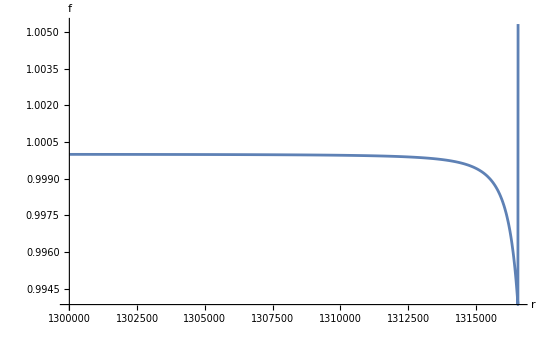

```mathematica
X1=Plot[f[r]/.rep,{r,1.30 10^6,1.316549372314* 10^6 }, PlotRange->All,AxesLabel->{Style[" r",FontSize->22],
Style["f", FontSize->22]}]
```

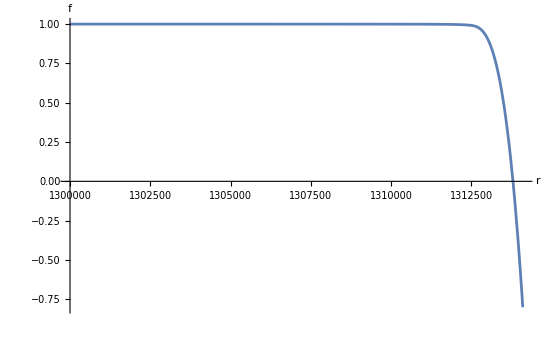

```mathematica
X2=Plot[f[r]/.rep,{r,1.3 10^6,1.3141* 10^6 }, PlotRange->All,AxesLabel->{Style[" r",FontSize->22],
Style["f", FontSize->22]}]
```